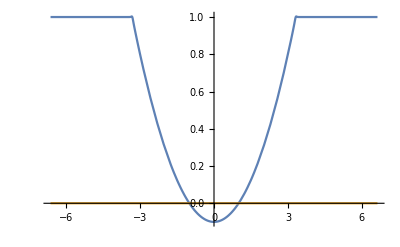

```mathematica
(*Configuration*)
a=0.1;
ν=0.0000001;
n=100.;

b=(1.+1./a)^(-n);
Epsilon = Function[x,1.+(a*(x^2.-1.)+ⅈ*ν-1.)/(1.+b*x^(2.n))];

X0=2.*Sqrt[1.+1./a];
Plot[{Re[Epsilon[x]],Im[Epsilon[x]]},{x,-X0,X0},PlotRange->Full]

A=1.;
```

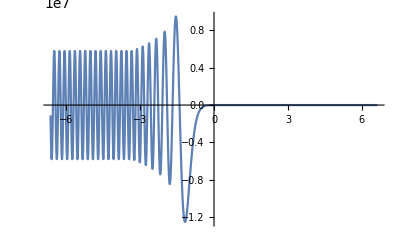

0.0000356109

```mathematica
(*TE-wave*)
ETEEquation={y''[x]+χ^2.*(Epsilon[x]-Sin[θ]^2.)*y[x]==0.};
ETEInitials={y[X0]==A,y'[X0]==ⅈ*χ*A} (* χ=k0*L, where L is a width of the layer *);

ETE=ParametricNDSolveValue[{ETEEquation,ETEInitials},y,{x,-X0,X0},{θ,χ}];
Plot[Re[ETE[0.,30.][x]],{x,-X0,X0},PlotRange->Full]

RTE=Function[{θ,χ},Exp[2.*ⅈ*χ*(-X0)]*(ⅈ*χ*ETE[θ,χ][-X0]-ETE[θ,χ]'[-X0])/(ⅈ*χ*ETE[θ,χ][-X0]+ETE[θ,χ]'[-X0])];
TTE=Function[{θ,χ},ETE[θ,χ][X0]*Exp[-ⅈ*χ*(X0)]*(Exp[ⅈ*χ*(-X0)]+RTE[θ,χ]*Exp[-ⅈ*χ*(-X0)])/ETE[θ,χ][-X0]];

TEDissipation =Function[{θ,χ},1. - Abs[RTE[θ,χ]]^2.-Abs[TTE[θ,χ]]^2.];
TEDissipation[0.,30.]
```

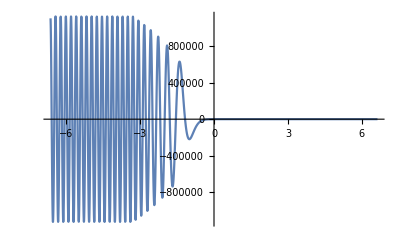

0.0000355848

```mathematica
(*TM-wave*)
BTMEquation={y''[x]-(Epsilon'[x]/Epsilon[x])*y'[x]+χ^2.*(Epsilon[x]-Sin[θ]^2.)*y[x]==0};
BTMInitials={y[X0]==-A,y'[X0]==-ⅈ*χ*Epsilon[X0]*A*Cos[θ]};

BTM=ParametricNDSolveValue[{BTMEquation,BTMInitials},y,{x,-X0,X0},{θ,χ}];
Plot[Re[BTM[0.,30.][x]],{x,-X0,X0},PlotRange->Full]

RTM=Function[{θ,χ},Exp[2.*ⅈ*χ*(-X0)]*(ⅈ*χ*BTM[θ,χ][-X0]-BTM[θ,χ]'[-X0])/(ⅈ*χ*BTM[θ,χ][-X0]+BTM[θ,χ]'[-X0])];
TTM=Function[{θ,χ},BTM[θ,χ][X0]*Exp[-ⅈ*χ*(X0)]*(Exp[ⅈ*χ*(-X0)]+RTM[θ,χ]*Exp[-ⅈ*χ*(-X0)])/BTM[θ,χ][-X0]];

TMDissipation=Function[{θ,χ},1.-Abs[RTM[θ,χ]]^2.-Abs[TTM[θ,χ]]^2.];
TMDissipation[0.,30.]
```

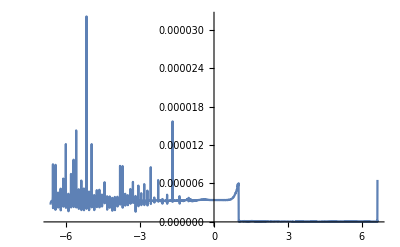

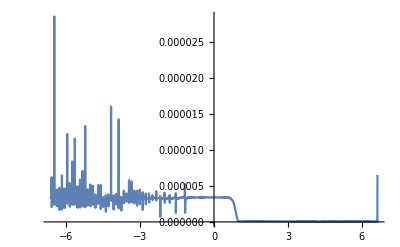

```mathematica
(*Reletive precision*)
values={θ->0.,χ->30.};
ETM=Function[x,ⅈ*BTM[θ,χ]'[x]/(χ*Epsilon[x])];
Plot[Abs[ETE[θ,χ][x]-ETM[x]]/Min[Abs[ETE[θ,χ][x]],Abs[ETM[x]]]/.values,{x,-X0,X0},PlotRange->Full]

BTE=Function[x,(-ⅈ/χ)*ETE[θ,χ]'[x]];
Plot[Abs[BTE[x]+BTM[θ,χ][x]]/Min[Abs[BTE[x]],Abs[BTM[θ,χ][x]]]/.values,{x,-X0,X0},PlotRange->Full]
```

```mathematica
limits={χ1->5.,χ2->50.};
Teta=Function[χ,Abs[θ/.NMaximize[TMDissipation[θ,χ],θ][[2]]]];
Data=Table[Teta[x],{x,χ1/.limits,χ2/.limits}];
```

{m→-0.347467,h→0.424015}

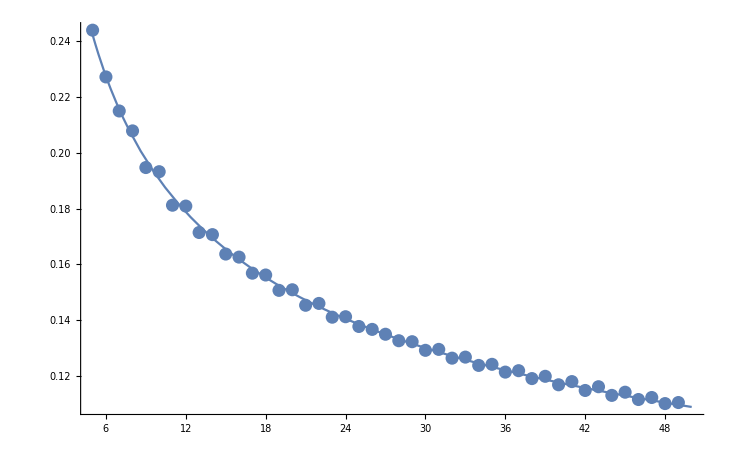

```mathematica
points=Table[Prepend[{Data[[i]]},i+(χ1-1)/.limits],{i,(χ2-χ1)/.limits}];
fit=FindFit[points,h*x^m,{m,h},x]
Experiment=ListPlot[points];
Approximation=Plot[(h*x^m)/.fit,{x,χ1/.limits,χ2/.limits}];
Show[Experiment,Approximation,PlotRange->Automatic]
```

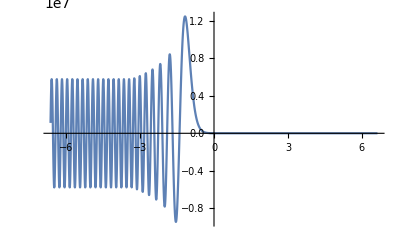

0.00402327

```mathematica
(*Anisotropy*)
V = Function[x, 1. - Epsilon[x]];
U = 10^(-3)(* U = |eB/(mcw)|, so for B~1000G U~10^(-10) *);
T={{ⅈ,-ⅈ,0},{1,1,0},{0,0,1}} (*Matrix to diagonalize permittivity*);
P[x_]=T.{{1-V[x]/(1+U),0,0},{0,1-V[x]/(1-U),0},{0,0,1-V[x]}}.Inverse[T] (*Permittivity, from diagonal to usual*);

GeneralSystem = {
(*Ex[x]*P[x][[1,1]]+Ey[x]*P[x][[1,2]]==kz*By[x]-ky*Bz[x],
Bx[x]==ky*Ez[x]-kz*Ey[x],*)
Ey'[x]==ⅈ*χ*(ky*(kz*By[x]-ky*Bz[x]-Ey[x]*P[x][[1,2]])/P[x][[1,1]]+Bz[x]),(*Ey'[x]==ⅈ*χ*(ky*Ex[x]+Bz[x])*)
Ez'[x]==ⅈ*χ*(kz*(kz*By[x]-ky*Bz[x]-Ey[x]*P[x][[1,2]])/P[x][[1,1]]-By[x]),(*Ez'[x]==ⅈ*χ*(kz*Ex[x]-By[x])*)
By'[x]==ⅈ*χ*(ky*(ky*Ez[x]-kz*Ey[x])-P[x][[3,3]]*Ez[x]),(*By'[x]==ⅈ*χ*(ky*Bx[x]-P[x][[3,3]]*Ez[x])*)
Bz'[x]==ⅈ*χ*(kz*(ky*Ez[x]-kz*Ey[x])+P[x][[2,1]]*(kz*By[x]-ky*Bz[x]-Ey[x]*P[x][[1,2]])/P[x][[1,1]]+P[x][[2,2]]*Ey[x])
(*Bz'[x]==ⅈ*χ*(kz*Bx[x]+P[x][[2,1]]*Ex[x]+P[x][[2,2]]*Ey[x])*)
}/.{kx->Sin[ϕ]Cos[θ],ky->Sin[ϕ]Sin[θ],kz->Cos[ϕ]};

GeneralInitials = { 
(*Ex[X0]==A*(Sin[θ]Sin[α]-Cos[ϕ]Cos[θ]Cos[α]),*)
Ey[X0]==-A*(Cos[θ]Sin[α]+Cos[ϕ]Sin[θ]Cos[α]),
Ez[X0]==A*Sin[ϕ]Cos[α],
(*Bx[X0]==A*(Sin[θ]Cos[α]+Cos[ϕ]Cos[θ]Sin[α]),*)
By[X0]==A*(Cos[ϕ]Sin[θ]Sin[α]-Cos[θ]Cos[α]),
Bz[X0]==-A*Sin[ϕ]Sin[α]
};

Solution = NDSolveValue[{GeneralSystem,GeneralInitials}/.{χ->30.,θ->0.,ϕ->π/2.,α->π/2},{Ey,Ez,By,Bz},{x,-X0,X0}];

Eτ=Function[x,If[Solution[[1]][X0]==0,Solution[[2]][x],Solution[[1]][x]/Cos[ArcTan[Abs[Solution[[2]][X0]]/Abs[Solution[[1]][X0]]]]]];
Plot[Re[Eτ[x]],{x,-X0,X0}]

R=Function[χ,Exp[2.*ⅈ*χ*(-X0)]*(ⅈ*χ*Eτ[-X0]-Eτ'[-X0])/(ⅈ*χ*Eτ[-X0]+Eτ'[-X0])];
T=Function[χ,Eτ[X0]*Exp[-ⅈ*χ*(X0)]*(Exp[ⅈ*χ*(-X0)]+R[χ]*Exp[-ⅈ*χ*(-X0)])/Eτ[-X0]];
Dissipation = Function[χ,1. - Abs[R[χ]]^2.-Abs[T[χ]]^2.];

Dissipation[30]
```

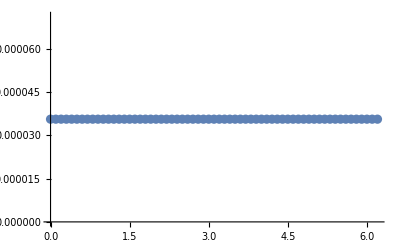

```mathematica
DissipationFromΑ={};
For[Α=0,Α<2π,Α+=0.1,
Solution = NDSolveValue[{GeneralSystem,GeneralInitials}/.{χ->30.,θ->0.,ϕ->π/2.,α->Α},{Ey,Ez,By,Bz},{x,-X0,X0}];
Eτ=Function[x,If[Solution[[1]][X0]==0,Solution[[2]][x],Solution[[1]][x]/Cos[ArcTan[Abs[Solution[[2]][X0]]/Abs[Solution[[1]][X0]]]]]];
R=Function[χ,Exp[2.*ⅈ*χ*(-X0)]*(ⅈ*χ*Eτ[-X0]-Eτ'[-X0])/(ⅈ*χ*Eτ[-X0]+Eτ'[-X0])];
T=Function[χ,Eτ[X0]*Exp[-ⅈ*χ*(X0)]*(Exp[ⅈ*χ*(-X0)]+R[χ]*Exp[-ⅈ*χ*(-X0)])/Eτ[-X0]];
Dissipation = Function[χ,1. - Abs[R[χ]]^2.-Abs[T[χ]]^2.];
DissipationFromΑ=Append[DissipationFromΑ,{Α,Dissipation[30]}];
];
ListPlot[DissipationFromΑ]
```

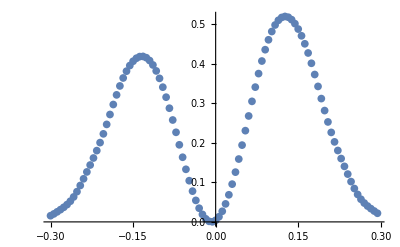

```mathematica
DissipationFromΘ={};
begining=-0.3; end=0.3; nstep=100.;
ProgressIndicator[Dynamic[(Θ-begining)/(end-begining)]]
For[Θ=begining,Θ<end,Θ+=(end-begining)/nstep,
Solution = NDSolveValue[{GeneralSystem,GeneralInitials}/.{χ->30.,θ->Θ,ϕ->π/2.,α->π/2},{Ey,Ez,By,Bz},{x,-X0,X0}];
Eτ=Function[x,If[Solution[[1]][X0]==0,Solution[[2]][x],Solution[[1]][x]/Cos[ArcTan[Abs[Solution[[2]][X0]]/Abs[Solution[[1]][X0]]]]]];
R=Function[χ,Exp[2.*ⅈ*χ*(-X0)]*(ⅈ*χ*Eτ[-X0]-Eτ'[-X0])/(ⅈ*χ*Eτ[-X0]+Eτ'[-X0])];
T=Function[χ,Eτ[X0]*Exp[-ⅈ*χ*(X0)]*(Exp[ⅈ*χ*(-X0)]+R[χ]*Exp[-ⅈ*χ*(-X0)])/Eτ[-X0]];
Dissipation = Function[χ,1. - Abs[R[χ]]^2.-Abs[T[χ]]^2.];
DissipationFromΘ=Append[DissipationFromΘ,{Θ,Dissipation[30]}];
];
ListPlot[DissipationFromΘ]
```